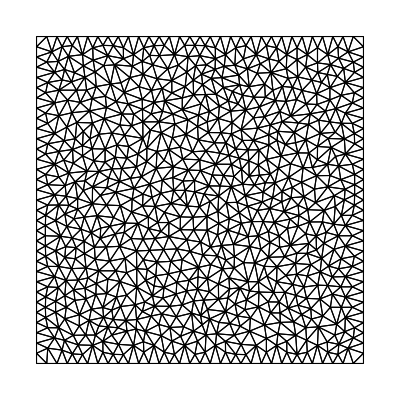

```mathematica
region=Rectangle[{0,0},{1,1}];
Needs["NDSolve`FEM`"];
h=0.001; 
(*Generate triangular mesh*)
em=ToElementMesh[region,"MeshOrder"->1,"MeshElementType"->"TriangleElement",MaxCellMeasure->h];

(*Extract mesh elements and nodes*)
elements=em["MeshElements"][[1,1]];
nodes=em["Coordinates"];
n=Length[elements];

(*Compute triangle centroids for labeling*)
(*centroids=Mean[nodes[[#]]]&/@elements;*)

(*Create text labels for each triangle*)
(*labels=MapThread[Text[Style[#1,12,Blue],#2]&,{Range[Length[elements]],centroids}];*)

(*Show mesh with labeled triangle indices*)
Show[em["Wireframe"](*,Graphics[labels]*)]
```

```mathematica
getShortestEdgeInMesh[nodes_,elements_]:=Module[{maxLen,temp,i,j,allNodes,maxi},(
maxLen=10;
maxi=-1;
For[i =n,i>0,i--,
For[j=1,j≤3,j++,
allNodes={1,2,3};
allNodes=DeleteCases[allNodes,j];
temp=EuclideanDistance[nodes[[elements[[i,allNodes[[1]]]]]],nodes[[elements[[i,allNodes[[2]]]]]]];If[temp<maxLen,maxLen=temp;maxi={i,j}]
]
];
maxLen
)]
```

```mathematica
minLen=getShortestEdgeInMesh[nodes,elements]
```

0.0280632

```mathematica
ρ[dots_]:=1.
μ[dots_]:=1.
λ[dots_]:=1.
```

```mathematica
(*Utils*)

(*Generates a map with key the index of an element in a triangle mesh and value array of indices of neighbouring elements ordered by their edge numbers
-1 if there is no neighbour for corresponding edge
*)
tri2Tri[nodes_,elements_]:=Module[{nt,np,neighbours, n2e,i,elementsWithNode1, elementsWithNode2, elementsWithNode3, elementsWithEdge1, elementsWithEdge2, elementsWithEdge3 },(
nt=Length[elements];
np=Length[nodes];
neighbours=Table[-1,nt,3];
n2e=GroupBy[Flatten[MapIndexed[#1->First[#2]&,elements,{2}],1],First->Last];
For[i=1,i<=nt,i++,
elementsWithNode1=Lookup[n2e,elements[[i,1]],{}];elementsWithNode2=Lookup[n2e,elements[[i,2]],{}];
elementsWithNode3=Lookup[n2e,elements[[i,3]],{}];
elementsWithEdge1 = DeleteCases[Intersection[elementsWithNode2, elementsWithNode3],i];
If[elementsWithEdge1 ≠ {},
neighbours[[i,1]]=elementsWithEdge1[[1]]
];
elementsWithEdge2=DeleteCases[Intersection[elementsWithNode1,elementsWithNode3],i];
If[elementsWithEdge2 ≠ {},
neighbours[[i,2]]=elementsWithEdge2[[1]]
];
elementsWithEdge3=DeleteCases[Intersection[elementsWithNode1,elementsWithNode2],i];
If[elementsWithEdge3 ≠ {},
neighbours[[i,3]]=elementsWithEdge3[[1]]
];
];
neighbours
)]

IsFreeSurface[dots_,nj_,j_]:=Module[{},(
If[nj=={0,1}&&dots[[j,2]]==1(*HARDCODED*),
True,
False]
)]

IsFreeSurfaceIrregularRegion[nj_]:=Module[{},(
If[nj[[2]]>0,
True,
False]
)]

getHatCoefficients[dots_]:=Module[{A,V},(
V=Table[If[j>1,dots[[i,j-1]] ,1],{i,1,3},{j,1,3}];
A=Inverse[V];
A
)]
precomputeHatCoefficients[nodes_,elements_]:=Module[{A,V,dots,nt,i},(
nt=Length[elements];
A=Table[0,nt,3,3];
For[i=1,i≤nt,i++,
dots=nodes[[elements[[i]]]];
A[[i]]=getHatCoefficients[dots]
];
A
)]


calculateLocalM0[dots_]:=Module[{j},(
j={{dots[[2,1]]-dots[[1,1]], dots[[2,2]]-dots[[1,2]]}, {dots[[3,1]]-dots[[1,1]], dots[[3,2]]-dots[[1,2]]}};
Det[j]*1./24*{{2.,1.,1.},{1.,2.,1.},{1.,1.,2.}}
)]

calculateLocalDα[dots_]:=Module[{dξ,dη,B,j,sj,Dx,Dy},(
dξ=1./6*{{-1,1,0},{-1,1,0},{-1,1,0}};
dη=1./6*{{-1,0,1},{-1,0,1},{-1,0,1}};
B={{ dots[[3,2]]-dots[[1,2]],-dots[[2,2]]+dots[[1,2]]},{-dots[[3,1]]+dots[[1,1]],dots[[2,1]]-dots[[1,1]]}};
j={{dots[[2,1]]-dots[[1,1]], dots[[2,2]]-dots[[1,2]]}, {dots[[3,1]]-dots[[1,1]], dots[[3,2]]-dots[[1,2]]}};
sj=Sign[Det[j]];
Dx=sj*(B[[1,1]]*dξ+B[[1,2]]*dη);
Dy=sj*(B[[2,1]]*dξ+B[[2,2]]*dη);
{Dx,Dy}
)]

trianglesMap={
1./6*{{0,0,0},{0,2,1},{0,1,2}},
1./6*{{2,0,1},{0,0,0},{1,0,2}},
1./6*{{2,1,0},{1,2,0},{0,0,0}}};

(*Rτk and Rτi are not equal when different polynomial degrees used for different elements*)
calculateLocalR[dots_, edgeNumber_]:=Module[{allNodes,lenOfEdge},(
allNodes={1,2,3};
allNodes = DeleteCases[allNodes,edgeNumber];
lenOfEdge=Sqrt[(dots[[allNodes[[1]],1]] - dots[[allNodes[[2]],1]])^2+(dots[[allNodes[[1]],2]] - dots[[allNodes[[2]],2]])^2];
lenOfEdge*trianglesMap[[edgeNumber]]
)]

getAx[ρ_,μ_,λ_]:=Module[{},(
{{0,0,1./ρ,0,0},{0,0,0,0,1./ρ},{2*μ+λ,0,0,0,0},{λ,0,0,0,0},{0,μ,0,0,0}}
)]
getAy[ρ_,μ_,λ_]:=Module[{},(
{{0,0,0,0,1./ρ},{0,0,0,1./ρ,0},{0,λ,0,0,0},{0,2*μ+λ,0,0,0},{μ,0,0,0,0}}
)]

getNormalVectorOfJthSide[dots_,j_]:=Module[{allNodes,coords,n,trialPoint1,trialPoint2,distVec1,distVec2},(
allNodes={1,2,3};
allNodes = DeleteCases[allNodes,j];
coords=dots[[allNodes[[1]]]]-dots[[allNodes[[2]]]];
n={-coords[[2]],coords[[1]]};
(*Equivalent approach;
trialPoint1=dots[[allNodes[[1]]]]+n;
trialPoint2=dots[[allNodes[[1]]]]-n;
distVec1=trialPoint1-dots[[j]];
distVec2=trialPoint2-dots[[j]];
(*if it is closer then it is negative the normal vector*)
If[distVec1[[1]]^2+distVec1[[2]]^2<distVec2[[1]]^2+distVec2[[2]]^2,n=-n];*)
If[Cos[PlanarAngle[{dots[[j]],dots[[allNodes[[1]]]],dots[[allNodes[[1]]]]+n}]]>0,n=-n];
n=n/Norm[n];
n
)]

precomputeEquationMatriciesForAllElements[elements_,nodes_,neighbours_]:=Module[{n,MassMatrices,StiffnessMatrices,loadVectorsMultipliers,i,j,dots,M0,M1x,M1y,StiffnessComponentsX,StiffnessComponentsY,StiffnessComponentsN,nj,MassMatricesOnEdges,Kp},(
n=Length[elements];
MassMatrices=Table[0,n,5*3,5*3];
StiffnessMatrices=Table[0,n,5*3,5*3];
(*For each element we have 3 potential sides and for each side we have a matrix*)
loadVectorsMultipliers=Table[0,n,3,5*3,5*3];
For[i=1,i≤n,i++,
dots=nodes[[elements[[i]]]];
M0=calculateLocalM0[dots];
MassMatrices[[i]]+=KroneckerProduct[IdentityMatrix[5],M0];
{M1x,M1y}=calculateLocalDα[dots];
StiffnessComponentsX=getAx[ρ[dots],μ[dots],λ[dots]];
StiffnessComponentsY=getAy[ρ[dots],μ[dots],λ[dots]];
StiffnessMatrices[[i]]-=KroneckerProduct[StiffnessComponentsX,M1x];
StiffnessMatrices[[i]]-=KroneckerProduct[StiffnessComponentsY,M1y];
For[j=1,j≤3,j++,
nj=getNormalVectorOfJthSide[dots,j];
StiffnessComponentsN=nj[[1]]*StiffnessComponentsX+nj[[2]]*StiffnessComponentsY;
MassMatricesOnEdges=calculateLocalR[dots,j];
If[neighbours[[i,j]]==-1,
If[IsFreeSurface[dots,nj,j],
StiffnessComponentFreeSurface = Table[0,5,5];
StiffnessComponentFreeSurface[[{1,2}]]=StiffnessComponentsN[[{1,2}]];
StiffnessMatrices[[i]]+=KroneckerProduct[StiffnessComponentFreeSurface,MassMatricesOnEdges],
StiffnessMatrices[[i]]+=KroneckerProduct[StiffnessComponentsN,MassMatricesOnEdges]
],
Kp=0.5*KroneckerProduct[StiffnessComponentsN,MassMatricesOnEdges];
StiffnessMatrices[[i]]+=Kp;
loadVectorsMultipliers[[i,j]]+=Kp;
]
]
];
{MassMatrices,StiffnessMatrices,loadVectorsMultipliers}
)]


eulerScheme[nodes_,elements_,τ_,Tmax_]:=Module[{MassMatrices,StiffnessMatrices,loadVectorsMultipliers,n,nextTimeStepCoefficient,currentTimeStepCoefficient,invLHS,coeffRHS,loadVectors,i,j,stepsCount},(
neighbours=tri2Tri[nodes,elements];
{MassMatrices,StiffnessMatrices,loadVectorsMultipliers}=precomputeEquationMatriciesForAllElements[elements,nodes,neighbours];
n=Length[elements];
stepsCount=Ceiling[Tmax/τ];
W=Table[0,stepsCount,n,5*3];
(*Подобрен Ойлер, като само Wk се смята САМО в предния слой по време*)
loadVectorsMultipliers*=2;
nextTimeStepCoefficient=2*MassMatrices-τ*StiffnessMatrices;
currentTimeStepCoefficient=2*MassMatrices+τ*StiffnessMatrices;
(*Ойлер с разлика назад*)
(*nextTimeStepCoefficient=MassMatrices;
currentTimeStepCoefficient=StiffnessMatrices+MassMatrices;*)

(*We have nextTimeStepCoefficient.W^(t+1)=currentTimeStepCoefficient.W^t+τ*loadVectorsMultipliers*)
invLHS=Table[0,n,5*3,5*3];
coeffRHS=Table[0,n,5*3,5*3];
For[i=1,i≤n,i++,
invLHS[[i]]=Inverse[nextTimeStepCoefficient[[i]]];
coeffRHS[[i]]=invLHS[[i]].currentTimeStepCoefficient[[i]];
];

(*Initial conditions*)
W[[1,989]]=Flatten[Table[{100.,100.,0.,0.,0.},3]];

For[t=1,t<stepsCount,t++,
For[i=1,i≤n,i++,
loadVectors=Table[0,n,5*3];
For[j=1,j≤3,j++,
(*ако neighbours[[i,j]] е -1, loadVectorsMultipliers[[i,j]] БИ ТРЯБВАЛО ДА е 0-ва матрица, so we are good*)
(*Dobavi GU-ta*)
loadVectors[[i]]+=τ*loadVectorsMultipliers[[i,j]].W[[t,neighbours[[i,j]]]];
];

W[[t+1,i]]=coeffRHS[[i]].W[[t,i]]+invLHS[[i]].loadVectors[[i]];
]
];
)]
```

```mathematica
(*LEAP FROG SCHEME*)
```

```mathematica
Print["LEAP FROG SHEME, DO NOT DELETE!"]

leapFrogScheme[nodes_,elements_,τ_,Tmax_]:=Module[{stepsCount,Av,Bv,Cv,Aσ,Bσ,Cσ,dots,Dx,Dy,Ax,Axv,Axσ,Ay,Ayv,Ayσ,i,j,nj,Anv,Anσ,R,Kpv,Kpσ,Wv,Wσ,t},(
neighbours=tri2Tri[nodes,elements];
stepsCount=Ceiling[Tmax/τ];
n=Length[elements];
Av=Table[0,n,3*2,3*2];
Bv=Table[0,n,3*2,3*3];
Cv=Table[0,n,3,3*2,3*3];

Aσ=Table[0,n,3*3,3*3];
Bσ=Table[0,n,3*3,3*2];
Cσ=Table[0,n,3,3*3,3*2];
For[i=1,i≤n,i++,
dots=nodes[[elements[[i]]]];
Av[[i]]+=KroneckerProduct[IdentityMatrix[2],calculateLocalM0[dots]];
Aσ[[i]]+=KroneckerProduct[IdentityMatrix[3],calculateLocalM0[dots]];

{Dx,Dy}=calculateLocalDα[dots];
Ax=getAx[ρ[dots],μ[dots],λ[dots]];
Axv=Ax[[{1,2},{3,4,5}]];
Axσ=Ax[[{3,4,5},{1,2}]];

Ay=getAy[ρ[dots],μ[dots],λ[dots]];
Ayv=Ay[[{1,2},{3,4,5}]];
Ayσ=Ay[[{3,4,5},{1,2}]];

Bv[[i]]-=KroneckerProduct[Axv,Dx];
Bv[[i]]-=KroneckerProduct[Ayv,Dy];

Bσ[[i]]-=KroneckerProduct[Axσ,Dx];
Bσ[[i]]-=KroneckerProduct[Ayσ,Dy];
For[j=1,j≤3,j++,
nj=getNormalVectorOfJthSide[dots,j];
Anv=nj[[1]]*Axv+nj[[2]]*Ayv;
Anσ=nj[[1]]*Axσ+nj[[2]]*Ayσ;
R=calculateLocalR[dots,j];
If[neighbours[[i,j]]==-1,
Bv[[i]]+=KroneckerProduct[Anv,R];
Bσ[[i]]+=KroneckerProduct[Anσ,R],
Kpv=0.5*KroneckerProduct[Anv,R];
Kpσ=0.5*KroneckerProduct[Anσ,R];
Bv[[i]]+=Kpv;
Bσ[[i]]+=Kpσ;
Cv[[i,j]]+=Kpv;
Cσ[[i,j]]+=Kpσ;
]
]
];
Wv=Table[0,stepsCount,n,3*2];
Wσ=Table[0,stepsCount,n,3*3];
(*Leap frog*)
mv=τ*Bv;
m=Table[0,n,5*3,5*3];
mσ=τ*Bσ;
Mv=Table[0,n,2*3,2*3];
Mσ=Table[0,n,3*3,3*3];
For[i=1,i≤n,i++,
Mv[[i]]=Inverse[Av[[i]]];
mv[[i]]=Mv[[i]].mv[[i]];
Mσ[[i]]=Inverse[Aσ[[i]]];
mσ[[i]]=Mσ[[i]].mσ[[i]];
];
Print["3"];
For[t=1,t<2,t++,
Fv=Table[0,n,2*3];
Fσ=Table[0,n,3*3];
For[i=1,i≤n,i++,
For[j=1,j≤3,j++,
(*ако neighbours[[i,j]] е -1, C[[i,j]] БИ ТРЯБВАЛО ДА е 0-ва матрица, so we are good*)
Fv[[i]]+=Cv[[i,j]].Wσ[[t,neighbours[[i,j]]]];
Fσ[[i]]+=Cσ[[i,j]].Wv[[t,neighbours[[i,j]]]];
];
If[t==1 && i==989,
(*TO DO: ADD INITIAL CONDITIONS*)
Fv[[i]]+=Flatten[Table[{100.,100.},3]];
Print[Fv[[i]]];
Print[Mv[[i]].Fv[[i]]]
];
Wv[[t+1,i]]=mv[[i]].Wσ[[t,i]]+Mv[[i]].Fv[[i]];
Wσ[[t+1,i]]=mσ[[i]].Wv[[t+1,i]]+Mσ[[i]].Fσ[[i]];
];
Print[Wv[[]]]
];
Print["4"];
Wv
)]
```

LEAP FROG SHEME, DO NOT DELETE!

```mathematica
(*FIND SUITABLE DOT FOR THE INITIAL CONDITIONS*)
For[i=1,i≤n,i++,
If[0.4<=nodes[[elements[[i,1]],1]]&&nodes[[elements[[i,1]],1]]≤0.6 &&0.4<=nodes[[elements[[i,2]],2]]&&nodes[[elements[[i,2]],2]]≤0.6,Print[i];Break[]]
]
```

989

```mathematica
(*IMPLEMENTATION WITH LOCAL MATRICIES*)
Tmax=0.2;
τ=0.0002;
eulerScheme[nodes,elements,τ,Tmax];
```

```mathematica
Dimensions[W]
```

{100,1602,15}

```mathematica
t
```

253

```mathematica
Y=Table[0,3*n];
X=Y;
i=elements[[All,1]];
j = elements[[All,2]];
k=elements[[All,3]];
X[[1;; ;;3]]=nodes[[i,1]];
X[[2;; ;;3]]=nodes[[j,1]];
X[[3;; ;;3]]=nodes[[k,1]];
Y[[1;; ;;3]]=nodes[[i,2]];
Y[[2;; ;;3]]=nodes[[j,2]];
Y[[3;; ;;3]]=nodes[[k,2]];


(*for euler*)
a=Table[Table[{X[[l+3*q]],Y[[l+3*q]],W[[10,q+1,5*l-4]]},{l,1,3}],{q,0,n-1}];


(*for leap frog*)
(*a=Table[Table[{X[[l+3*q]],Y[[l+3*q]],W[[3,q+1,l]]},{l,1,3}],{q,0,n-1}];*)






Length[X]
```

4806

```mathematica
Dimensions[W]
```

{20,1602,15}

```mathematica
(*for euler*)
a=Table[Table[{X[[l+3*q]],Y[[l+3*q]],W[[500,q+1,5*l-4]]},{l,1,3}],{q,0,n-1}];

(*for leap frog*)
(*a=Table[Table[{X[[l+3*q]],Y[[l+3*q]],W[[3,q+1,l]]},{l,1,3}],{q,0,n-1}];*)ListPlot3D[a,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*all schemes are divergent, so we should test for element number 989 where the initial conditions are*)
dots=nodes[[elements[[989]]]]
j={{dots[[2,1]]-dots[[1,1]], dots[[2,2]]-dots[[1,2]]}, {dots[[3,1]]-dots[[1,1]], dots[[3,2]]-dots[[1,2]]}}
Det[j]
Det[j]*1./24
calculateLocalM0[dots]
Inverse[calculateLocalM0[dots]].{1,1,1}
```

{{0.478726,0.447228},{0.521063,0.450087},{0.4979,0.478888}}

{{0.0423366,0.00285872},{0.0191739,0.0316606}}

0.00128559

0.0000535661

{{0.000107132,0.0000535661,0.0000535661},{0.0000535661,0.000107132,0.0000535661},{0.0000535661,0.0000535661,0.000107132}}

{4667.13,4667.13,4667.13}

```mathematica
Total[Total[W[[1]]]]
Total[Total[W[[2]]]]
t
```

600.

599.964

1000

```mathematica
For[ii=1,ii<10,ii++,
Print[Total[Total[W[[ii]]]]/Total[Total[W[[ii+1]]]]]
]
```

1.00006

1.001

1.00192

1.00284

1.00374

1.00463

1.00551

1.00638

1.00724

```mathematica
(*IMPLEMENTATION WITH GLOBAL MATRICIES*)
precomputeInvM0[nodes_,elements_]:=Module[{i,dots,res},(
res=Table[0,Length[elements],3,3];
For[i=1,i≤Length[elements],i++,
dots=nodes[[elements[[i]]]];
res[[i]]=Inverse[calculateLocalM0[dots]];
];
res
)]
precomputeAxAy[ρ_,μ_,λ_,nodes_,elements_]:=Module[{Ax,Ay,dots,i},(
Ax=Table[0,Length[elements],3,3];
For[i=1,i≤Length[elements],i++,
dots=nodes[[elements[[i]]]];
Ax[[i]]=getAx[ρ,μ,λ];
Ay[[i]]=getAy[ρ,μ,λ];
];
{Ax,Ay}
)]
precomputeAn[ρ_,μ_,λ_,nodes_,elements_]:=Module[{An,i,j,coords,n},(
(*per element per edge we have An*)
An=Table[0,Length[elements],3,3,3];
For[i=1,i≤Length[elements],i++,
dots=nodes[[elements[[i]]]];
For[j=1,j≤3,j++,
n=getNormalVectorOfJthSide[dots,j];
An[[i,j]]=n[[1]]*getAx[ρ,μ,λ]+getAy[ρ,μ,λ]*n[[2]];
];
];
)]
assembleGlobalMatricies[elements_, nodes_, neighbours_]:=Module[{R,Mx,My,M0,degreesOfFreedom,numberOfElements,ind,indk,dots,k,locR},(
Print["Function is not up to date with helper functions"];
Return[-1];
numberOfElements=Length[elements];
degreesOfFreedom=3;
M0=Table[0,degreesOfFreedom*numberOfElements,degreesOfFreedom*numberOfElements];
Mx=M0;
My=M0;
R=M0;
For[i=1,i<=numberOfElements,i++,
ind={3*i-2,3*i-1,3*i};
dots=nodes[[elements[[i]]]];
M0[[ind,ind]]+=calculateLocalM0[dots];
{Mx[[ind,ind]],My[[ind,ind]]}+=calculateLocalDα[dots];
For[j=1,j≤3(*smeni da e generic?*), j++,
locR=calculateLocalR[dots,j];
k=neighbours[[i, j]];
If[k ≠ -1, (*tuk osrednqvame, inache ne osrednqvame*)
R[[ind,ind]]+=0.5*locR;
indk={3*k-2,3*k-1,3*k};
R[[indk,indk]]+=0.5*locR,
R[[ind,ind]]+=locR;
]
]
];
)]

findWi[prevWi_,Wk_,dots_, precomputedInvM0_,precomputedAx_,precomputedAy_,precomputedAns_,dt_,i_]:=Module[{rhs,nhbrs,j,Dx,Dy},(
{Dx,Dy}=calculateLocalDα[dots];
rhs=-1*(precomputedAx.prevWi.Dx+precomputedAy.prevWi.Dy);
nhbrs=neighbours[[i]];
For[j=1,j≤3,j++,
If[nhbrs[[j]]==-1,
(*ili [[i,j]], zavisi kak se podavat, zasega bih podal na funkciqta samo an za i*)
rhs+=precomputedAns[[j]].prevWi.calculateLocalR[dots,j],
rhs+=0.5*precomputedAns[[j]].(prevWi.calculateLocalR[dots,j]+Wk.calculateLocalR[dots,j])
]
];
rhs+=F;
res=prevWi+dt*precomputedInvM0.rhs

)]
```